```mathematica
OS="win";(*or,linux*)
Needs["ErrorBarPlots`"];
Needs["EDA`"];
Needs["CustomTicks`"];
SetOptions[LinTicks,TickLabelStep->1,MajorTickLength->{0.0125,0},MinorTickLength->{0.0075,0}];
If[OS=="win",
Print["Working Directory: ",descDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\analysis-mirror_neutrons\\nstar_online"];Print["(AscDir) Rawdata Directory: ",AscDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\rawdata"];Print["(ScrDir) Scratch Directory: ",curDir=SetDirectory["C:\\Users\\tmpra\\Dropbox\\Scratch"]];Print["(PicDir) Picture Directory: ",PicDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\Pictures\\nstar\\runs2"];Print["(SysDir) System Directory: ",SysDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\system"];
Print["Rawdata on mpc1636:",mpcDir="/xdata/nedm_data/RawData"];
seperator="\\";
];
If[OS=="axion",
Print["Working Directory: ",descDir="/home/prajwal/Dropbox/nEDM/analysis-mirror_neutrons/nstar_online"];Print["(AscDir) Rawdata Directory: ",AscDir="/home/prajwal/Dropbox/nEDM/rawdata"];Print["(ScrDir) Scratch Directory: ",curDir=SetDirectory["/home/prajwal/Dropbox/Scratch"]];Print["(PicDir) Picture Directory: ",PicDir="/home/prajwal/Dropbox/nEDM/Pictures/nstar/runs"];Print["(SysDir) System Directory: ",SysDir="/home/prajwal/Dropbox/nEDM/system"];
Print["Rawdata on mpc1636:",mpcDir="/xdata/nedm_data/RawData"];
seperator="/";
];
metaStructure={Word,Real,Real,Word,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real};
metadesc={Number,Number,Number,Number,Number,Number,Number,Word,Real,Real,Real,Real};
descdat=ReadList[StringJoin[descDir,seperator,"desctf_c.dat"],metadesc];
dimdesc=Dimensions[descdat][[1]];
```

Working Directory: C:\Users\tmpra\Dropbox\nEDM\daq-tools-bkg-auto\nstar_online

(AscDir) Rawdata Directory: C:\Users\tmpra\Dropbox\nEDM\rawdata

(ScrDir) Scratch Directory: C:\Users\tmpra\Dropbox\Scratch

(PicDir) Picture Directory: C:\Users\tmpra\Dropbox\nEDM\Pictures\nstar\runs2

(SysDir) System Directory: C:\Users\tmpra\Dropbox\nEDM\system

Rawdata on mpc1636:/xdata/nedm_data/RawData

```mathematica
Monitor[
runndat={};
runbdat={};
runbdatwc={};
b0[i0_]:=0.0599624 i0 +0.000159804;
For[i=1,i≤dimdesc,i++,
Print[i,"   ",dimdesc];
Print[descdat[[i]][[4]]];
runndat=ReadList[StringJoin[AscDir,seperator,IntegerString[descdat[[i]][[4]],10,6],seperator,IntegerString[descdat[[i]][[4]],10,6],"_Meta5-2.dat"],metaStructure];
runbdatwc=ReadList[StringJoin[AscDir,seperator,IntegerString[descdat[[i]][[4]],10,6],seperator,IntegerString[descdat[[i]][[4]],10,6],"-0_B0HighCurrentReadout3.edm"],{Word,Real,Real,Number}];
(**1**)
runbdat=Select[runbdatwc,#[[2]]<.4&];
If[i==1,timeini=AbsoluteTime[runndat[[1]][[1]]]];
(**2**)
dimrun=Dimensions[runndat][[1]];
abstime=(AbsoluteTime/@runbdat[[;;,1]]);
endtm=110+descdat[[i]][[7]];
(**3**)
lvl1=Table[{0,0,0,0,0},{k,1,dimrun}];
For[j=1,j≤dimrun,j++,
inipos=Position[abstime,Nearest[abstime,AbsoluteTime[runndat[[j]][[1]]]][[1]]][[1]][[1]];
finpos=Position[abstime,Nearest[abstime,AbsoluteTime[runndat[[j]][[1]]]+endtm][[1]]][[1]][[1]];
totcou=PlusMinus[runndat[[j]][[27]]+runndat[[j]][[28]],Sqrt[runndat[[j]][[27]]+runndat[[j]][[28]]]];
moncou=PlusMinus[runndat[[j]][[30]],Sqrt[runndat[[j]][[30]]]];
magfield=b0[PlusMinus[Mean[runbdat[[inipos;;finpos,2]]],Sqrt[StandardDeviation[runbdat[[inipos;;finpos,2]]]^2+Mean[runbdat[[inipos;;finpos,3]]]^2]]];
lvl1[[j]]={N[AbsoluteTime[runndat[[j]][[1]]]+(endtm/2)],
(totcou/moncou)[[1]],
(totcou/moncou)[[2]],
magfield[[1]],
magfield[[2]]
};
];
Export[StringJoin[AscDir,seperator,IntegerString[descdat[[i]][[4]],10,6],seperator,IntegerString[descdat[[i]][[4]],10,6],"_lvl1.dat"],lvl1];
];,
ProgressIndicator[i/dimdesc,ImageSize->{1000,100}]
];
ProgressIndicator[1,ImageSize->{1000,100}]
```

1   40

12693

2   40

12695

StandardDeviation::shlen: The argument {0.170032} should have at least two elements.

General::stop: Further output of StandardDeviation::shlen will be suppressed during this calculation.

3   40

12697

4   40

12704

5   40

12707

6   40

12770

7   40

12771

8   40

12772

9   40

12773

10   40

12774

11   40

12775

12   40

12778

13   40

12779

14   40

12780

15   40

12781

16   40

13099

17   40

13101

18   40

13102

19   40

13103

20   40

13104

21   40

13105

22   40

13106

23   40

13107

24   40

13108

25   40

13109

26   40

13110

27   40

13111

28   40

13112

29   40

13132

30   40

13133

31   40

13134

32   40

13135

33   40

13136

34   40

13137

35   40

13138

36   40

13139

37   40

13140

38   40

13141

39   40

13142

40   40

13146

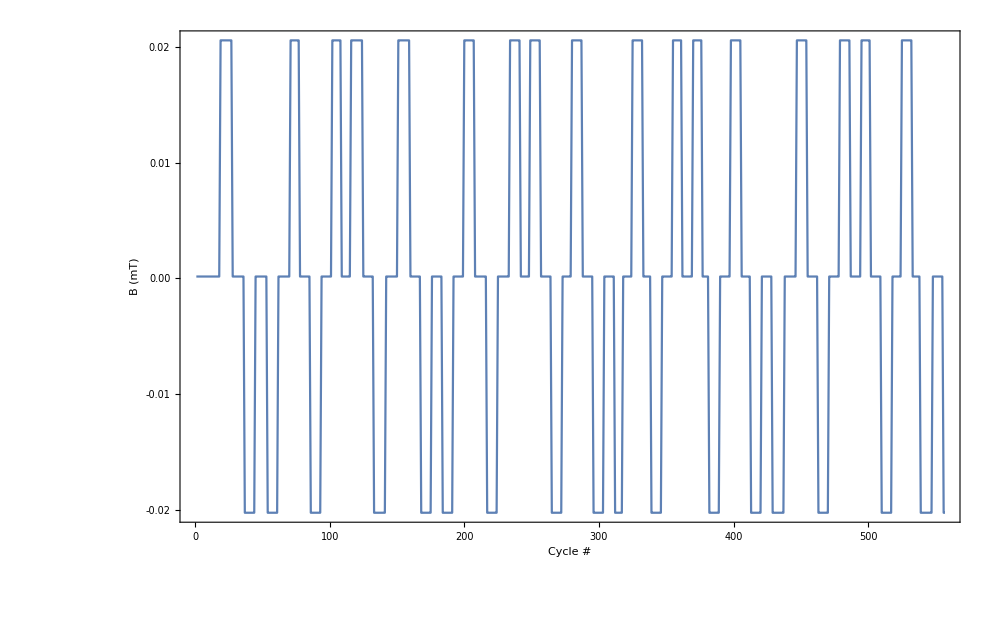

```mathematica
ListLinePlot[lvl1[[;;,4]],FrameLabel->{"Cycle #","B (mT)"},PlotRange->Full,TicksStyle->Directive[FontSize->40],Axes->None,AxesStyle->Thick,Frame->{True,True,True,True},FrameStyle->Thick,LabelStyle->{28,Black,Bold},ImageSize->1000,FrameTicks->LinTicks]
```

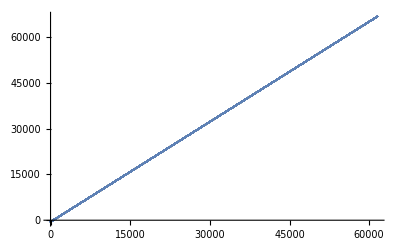

```mathematica
ListPlot[abstime]
```